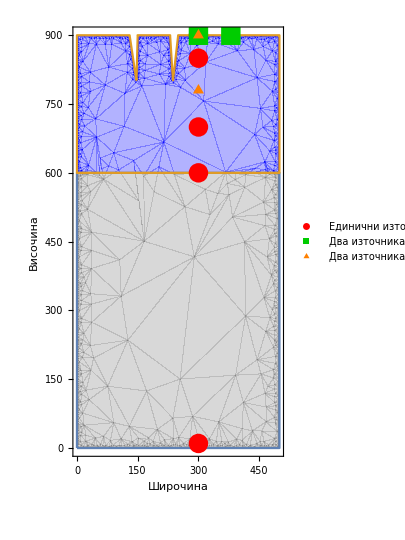

```mathematica
pointArrays={{{300,10},{300,600},{300,700},{300,850}, {300,900}},(*Array 1-lower region*){{380,900},{300,900}},(*Array 2-lower region*){{300,900},{300,780}}};

(*Define colors for each array*)
colors={RGBColor[1,0,0],(*Bright Red*)RGBColor[0,0.8,0],(*Green*)RGBColor[1,0.5,0],(*Orange*)RGBColor[0.5,0,1],(*Purple*)RGBColor[0,0.6,1],(*Light Blue*)RGBColor[0.8,0.2,0.8]   (*Magenta*)};
labels={"Единични източници с една пукнатина или без пукнатина", "Два източника при празни пукнатини", "Два източника при пукнатини, пълни с вода или въздух"};

region=Rectangle[{0,0},{500,900}];
polygonVertices1={{150,900},{147,800},{130,900}};
cavity1=Polygon[polygonVertices1];
polygonVertices2={{250,900},{237,800},{230,900}};
cavity2=Polygon[polygonVertices2];
regionWithCavity=RegionDifference[region,cavity1];
regionWithCavity=RegionDifference[regionWithCavity,cavity2];
Show[RegionPlot[{0≤x≤500&&0≤y<600,0≤x≤500&&600≤y≤900},{x,y }∈regionWithCavity,PlotStyle->{Opacity[0.3,Gray],Opacity[0.3,Blue]},Frame->True,FrameLabel->{"Широчина","Височина"}],ListPlot[pointArrays,PlotStyle->colors,PlotMarkers->{{"●",Large},{"■",Large},{"▲",Medium}},PlotLegends->labels],PlotRange->{{0,500},{0,900}},AspectRatio->900/500,ImageSize->300]
```

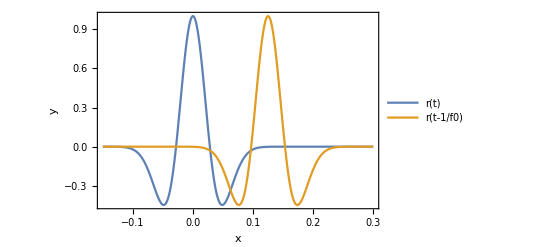

```mathematica
ricker[t_,f0_]:=Module[{a,tshift},(
tshift=1/f0;
a=Pi*f0*(t-tshift);
(1-2*a^2)*Exp[-a^2]
)]

Plot[{(1-2*Pi^2*64*t^2)*E^(-Pi^2*64*t^2),ricker[t,8]},{t,-0.15,0.3},PlotRange->All,Frame->True, FrameLabel->{"x","y"},PlotLegends->{"r(t)","r(t-1/f0)"}]
```

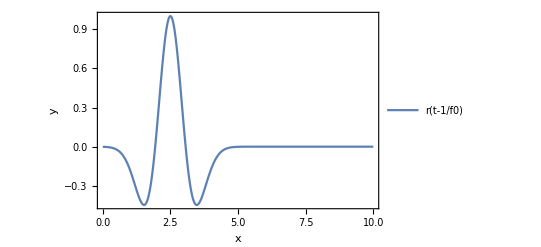

```mathematica
Plot[ricker[t,0.4],{t,0,10},PlotRange->All,Frame->True, FrameLabel->{"x","y"},PlotLegends->{"r(t-1/f0)"}]
```

```mathematica
tau=0.0248332
```

0.0248332

```mathematica
81*tau
```

2.01149

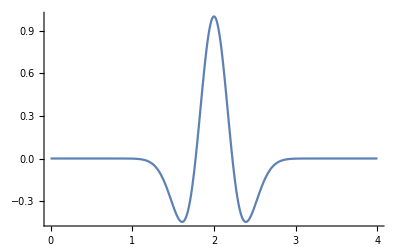

```mathematica
Plot[ricker[t,1],{t,0,4},PlotRange->All]
```

```mathematica
ricker[81*tau,1]
```

0.994736

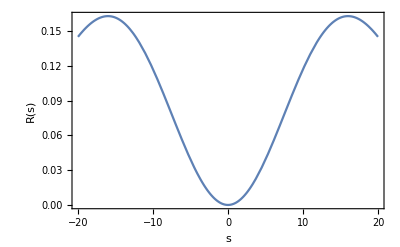

```mathematica
Plot[s^2*Sqrt[Pi]*E^(-s^2/(4f^2))/(2*f^3),{s,-20,20},Frame->True, FrameLabel->{"s","R(s)"}]
```

```mathematica
f
```

8

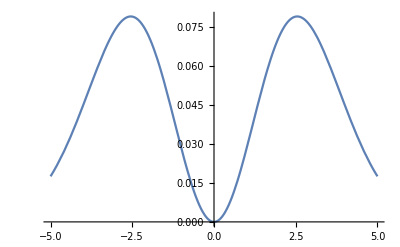

```mathematica
rickerFT[s_,f0_]:=2 Sqrt[2/E] Pi^2 s^2/f0^3 Exp[-Pi^2 s^2/f0^2]
Plot[rickerFT[s,8],{s,-5,5}]
```

```mathematica
Abs[rickerFTExpr/.s->2]
```

0.0283114

```mathematica
Expand[ricker[t,f]]
N[2*Pi^2]-1
-D[D[E^(-t^2/(2*s^2)),t],t]
```

-18.7392 ⅇ^(-f^2 π^2 (-1./f+t)^2)+39.4784 ⅇ^(-f^2 π^2 (-1./f+t)^2) f t-2 ⅇ^(-f^2 π^2 (-1./f+t)^2) f^2 π^2 t^2

18.7392

(ⅇ^(-t^2/(2 s^2)))/s^2-(ⅇ^(-t^2/(2 s^2)) t^2)/s^4

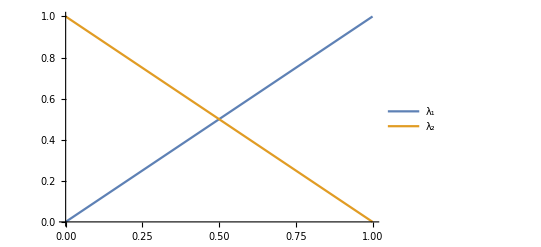

```mathematica
Plot[{x,1-x},{x,0,1},PlotLegends->{Subscript[λ,1],Subscript[λ,2]}]
```

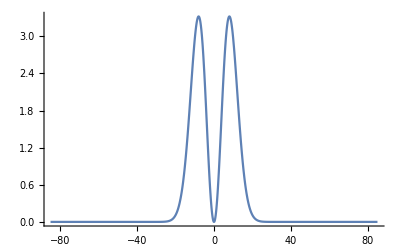

```mathematica
f=8;
Plot[2*s^2*E^(-s^2/f^2)/(Sqrt[Pi]*f),{s,-85,85},PlotRange->All]
```

```mathematica
Plot3D[{1-x-y,x,y},{x,0,1},{y,0,1-x},PlotLegends->{Subscript[λ,1],Subscript[λ,2],Subscript[λ,2]}]
```

-Graphics3D-

-Graphics3D-

(1 | 2 | 4
2 | 5 | 4
2 | 3 | 5
3 | 6 | 5
4 | 5 | 7
5 | 8 | 7
5 | 6 | 8
6 | 9 | 8)

(0 | 0
1 | 0
2 | 0
0 | 1
1 | 1
2 | 1
0 | 2
1 | 2
2 | 2)

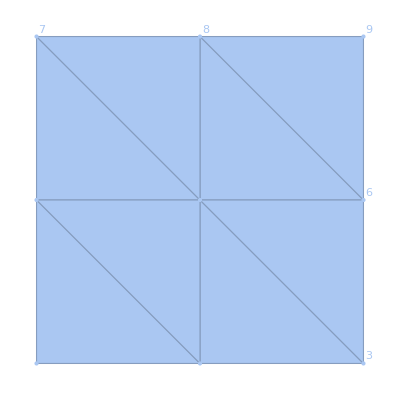

```mathematica
P=Transpose[{{0,1,2,0,1,2,0,1,2},{0,0,0,1,1,1,2,2,2}}];
T=Transpose[{{1,2,2,3,4,5,5,6},{2,5,3,6,5,8,6,9},{4,4,5,5,7,7,8,8}}];
MatrixForm[T]
MatrixForm[P]
El=Triangle[{{0,0},{0,1},{1,0}}];
Ω=MeshRegion[P,Triangle[T]];
HighlightMesh[Ω,Labeled[0,"Index"]]
```

```mathematica
Ihat[p_, t_, i_,x_] := Module[{res,r,a,b,c},(
res=0;
For[j=1,j≤Length[t],j++,
If[RegionMember[Triangle[p[[t[[j]]]]],x]&& MemberQ[t[[j]],i],
r=Position[t[[j]],i][[1,1]];
{a,b,c}=LinearSolve[{Insert[p[[t[[j]]]][[1]],1,3],Insert[p[[t[[j]]]][[2]],1,3],Insert[p[[t[[j]]]][[3]],1,3]},IdentityMatrix[3][[r]]];
res=a*x[[1]]+b*x[[2]]+c;
Break[];
];
];
res
)]
```

```mathematica
Plot3D[Ihat[P,T,5,{x,y}], {x,y}∈Ω,PlotStyle->Green]
```

-Graphics3D-